```mathematica
Clear["Global`*"]
```

```mathematica
imag=y μ^3-2 x y μ^3-2 x y μ^4+6 x^2 y μ^4-4 x^3 y μ^4-2 y^3 μ^4+4 x y^3 μ^4-2 x y μ^5+6 x^2 y μ^5-4 x^3 y μ^5-2 y^3 μ^5+4 x y^3 μ^5+6 x^2 y μ^6-24 x^3 y μ^6+30 x^4 y μ^6-12 x^5 y μ^6-2 y^3 μ^6+24 x y^3 μ^6-60 x^2 y^3 μ^6+40 x^3 y^3 μ^6+6 y^5 μ^6-12 x y^5 μ^6-4 x^3 y μ^7+20 x^4 y μ^7-36 x^5 y μ^7+28 x^6 y μ^7-8 x^7 y μ^7+4 x y^3 μ^7-40 x^2 y^3 μ^7+120 x^3 y^3 μ^7-140 x^4 y^3 μ^7+56 x^5 y^3 μ^7+4 y^5 μ^7-36 x y^5 μ^7+84 x^2 y^5 μ^7-56 x^3 y^5 μ^7-4 y^7 μ^7+8 x y^7 μ^7;

real = x μ^3-x^2 μ^3+y^2 μ^3-x^2 μ^4+2 x^3 μ^4-x^4 μ^4+y^2 μ^4-6 x y^2 μ^4+6 x^2 y^2 μ^4-y^4 μ^4-x^2 μ^5+2 x^3 μ^5-x^4 μ^5+y^2 μ^5-6 x y^2 μ^5+6 x^2 y^2 μ^5-y^4 μ^5+2 x^3 μ^6-6 x^4 μ^6+6 x^5 μ^6-2 x^6 μ^6-6 x y^2 μ^6+36 x^2 y^2 μ^6-60 x^3 y^2 μ^6+30 x^4 y^2 μ^6-6 y^4 μ^6+30 x y^4 μ^6-30 x^2 y^4 μ^6+2 y^6 μ^6-x^4 μ^7+4 x^5 μ^7-6 x^6 μ^7+4 x^7 μ^7-x^8 μ^7+6 x^2 y^2 μ^7-40 x^3 y^2 μ^7+90 x^4 y^2 μ^7-84 x^5 y^2 μ^7+28 x^6 y^2 μ^7-y^4 μ^7+20 x y^4 μ^7-90 x^2 y^4 μ^7+140 x^3 y^4 μ^7-70 x^4 y^4 μ^7+6 y^6 μ^7-28 x y^6 μ^7+28 x^2 y^6 μ^7-y^8 μ^7;
```

```mathematica
re1= Normal[Series[real,{y,0,2}]]
```

x μ^3-x^2 μ^3-x^2 μ^4+2 x^3 μ^4-x^4 μ^4-x^2 μ^5+2 x^3 μ^5-x^4 μ^5+2 x^3 μ^6-6 x^4 μ^6+6 x^5 μ^6-2 x^6 μ^6-x^4 μ^7+4 x^5 μ^7-6 x^6 μ^7+4 x^7 μ^7-x^8 μ^7+y^2 (μ^3+μ^4-6 x μ^4+6 x^2 μ^4+μ^5-6 x μ^5+6 x^2 μ^5-6 x μ^6+36 x^2 μ^6-60 x^3 μ^6+30 x^4 μ^6+6 x^2 μ^7-40 x^3 μ^7+90 x^4 μ^7-84 x^5 μ^7+28 x^6 μ^7)

```mathematica
Collect[re1/. y-> 0,x]
```

x μ^3+4 x^7 μ^7-x^8 μ^7+x^2 (-μ^3-μ^4-μ^5)+x^3 (2 μ^4+2 μ^5+2 μ^6)+x^6 (-2 μ^6-6 μ^7)+x^4 (-μ^4-μ^5-6 μ^6-μ^7)+x^5 (6 μ^6+4 μ^7)

```mathematica
im1= Normal[Series[imag,{y,0,2}]]
```

y (μ^3-2 x μ^3-2 x μ^4+6 x^2 μ^4-4 x^3 μ^4-2 x μ^5+6 x^2 μ^5-4 x^3 μ^5+6 x^2 μ^6-24 x^3 μ^6+30 x^4 μ^6-12 x^5 μ^6-4 x^3 μ^7+20 x^4 μ^7-36 x^5 μ^7+28 x^6 μ^7-8 x^7 μ^7)

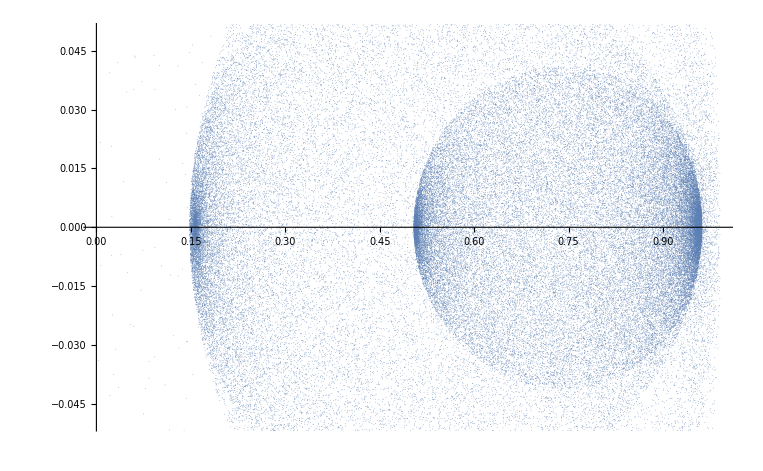
```mathematica
nuvem=Show[-Graphics-,Frame-> True];
```

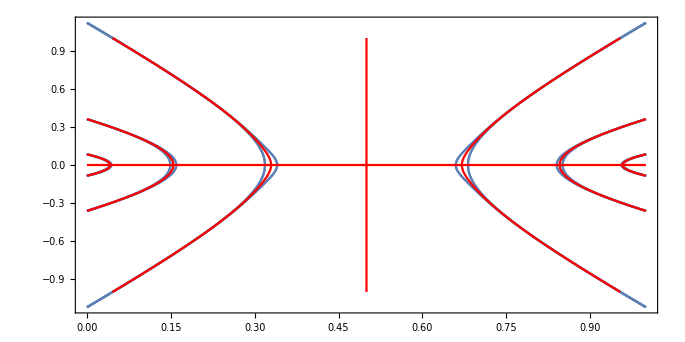
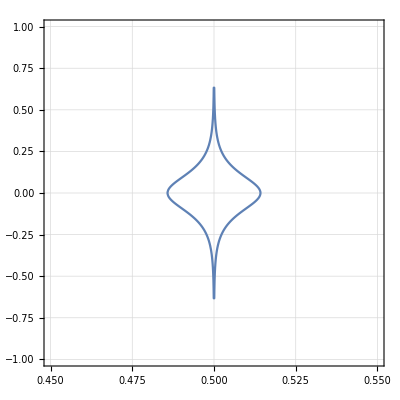
```mathematica
bands=Show[-Graphics-,-Graphics-];
```

```mathematica
Collect[real/. y-> 0,x]
```

x μ^3+4 x^7 μ^7-x^8 μ^7+x^2 (-μ^3-μ^4-μ^5)+x^3 (2 μ^4+2 μ^5+2 μ^6)+x^6 (-2 μ^6-6 μ^7)+x^4 (-μ^4-μ^5-6 μ^6-μ^7)+x^5 (6 μ^6+4 μ^7)

```mathematica
rea=Normal[Series[real/. y-> 0,{x,0.15,2}]]
reb=Normal[Series[real/. y-> 0,{x,0.5,2}]]
rec=Normal[Series[real/. y-> 0,{x,0.95,2}]]
```

0.1275 μ^3-0.0162563 μ^4-0.0162563 μ^5+0.00414534 μ^6-0.000264266 μ^7+(-0.15+x)^2 (-μ^3-0.235 μ^4-0.235 μ^5+0.277312 μ^6-0.0395027 μ^7)+(-0.15+x) (0.7 μ^3-0.1785 μ^4-0.1785 μ^5+0.0682763 μ^6-0.00580348 μ^7)

0.25 μ^3-0.0625 μ^4-0.0625 μ^5+0.03125 μ^6-0.00390625 μ^7+(-0.5+x)^2 (-μ^3+0.5 μ^4+0.5 μ^5-0.375 μ^6+0.0625 μ^7)

0.0475 μ^3-0.00225625 μ^4-0.00225625 μ^5+0.000214344 μ^6-5.09066×10^-6 μ^7+(-0.95+x)^2 (-μ^3-0.715 μ^4-0.715 μ^5+0.217313 μ^6-0.0105367 μ^7)+(-0.95+x) (-0.9 μ^3+0.0855 μ^4+0.0855 μ^5-0.0121837 μ^6+0.000385819 μ^7)

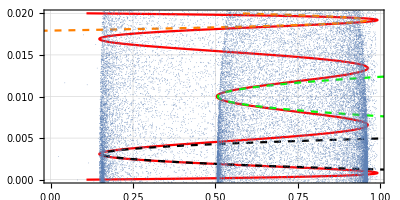

```mathematica
Show[ParametricPlot[{real/. {y-> 0.01, μ-> 3.82830},0.02x},{x,0,1},Frame->True,GridLines->Automatic,PlotStyle->Red],
ParametricPlot[{{rea/. μ-> 3.8283,0.02x},{reb/. μ-> 3.8283,0.02x},{rec/. μ-> 3.8283,0.02x}},{x,0,1},PlotStyle->{{Black,Dashed},{Green,Dashed},{Orange,Dashed}}],
nuvem,AspectRatio-> 1/2]
```

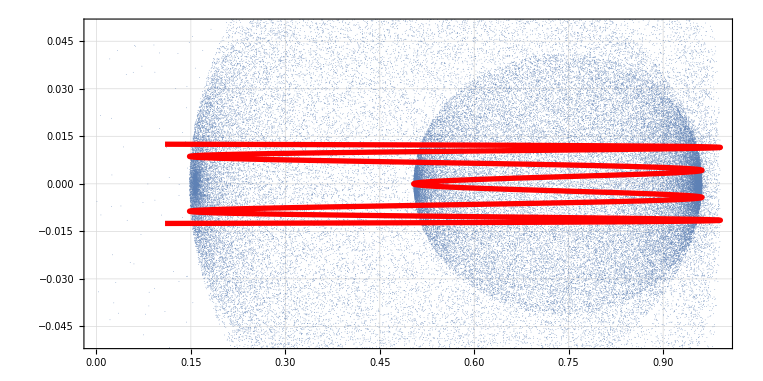

```mathematica
Show[nuvem,ParametricPlot[{real/. {y-> 0.01, μ-> 3.82830},1/40(x-0.5)},{x,0,1},Frame->True,PlotStyle->{Red,Thickness[0.005]},PlotRange->Automatic],AspectRatio-> 1/2,GridLines->Automatic]
```

```mathematica
Show[nuvem,ParametricPlot[{imag/. {μ-> 3.82830},y},{y,-0.01,0.01},{x,0,1},Frame->True,GridLines->Automatic,PlotStyle->Red],nuvem,AspectRatio-> 1/2]
```

-Graphics-

```mathematica
map1= ComplexExpand[r (x+ⅈ y) (1- (x+ⅈ y))]
```

r x-r x^2+r y^2+ⅈ (r y-2 r x y)

```mathematica
Solve[yn1==r y-2 r x y,y]
```

{{y→-yn1/(r (-1+2 x))}}

```mathematica
lista=Solve[xn1==r x-r x^2+r y^2/. y->-yn1/(r (-1+2 x)),x]
```

{{x→1/2 (1-(√(1-(4 xn1)/r-(√(r^2-8 r xn1+16 xn1^2+16 yn1^2))/r))/(√2))},{x→1/2 (1+(√(1-(4 xn1)/r-(√(r^2-8 r xn1+16 xn1^2+16 yn1^2))/r))/(√2))},{x→1/2 (1-(√(1-(4 xn1)/r+(√(r^2-8 r xn1+16 xn1^2+16 yn1^2))/r))/(√2))},{x→1/2 (1+(√(1-(4 xn1)/r+(√(r^2-8 r xn1+16 xn1^2+16 yn1^2))/r))/(√2))}}

```mathematica
Chop[lista⟦All,1,2⟧/. {r-> 3.8283,xn1-> 0.51,yn1-> 0},10^-6]
```

{0.5,0.5,0.158267,0.841733}

```mathematica
Chop[lista⟦All,1,2⟧/. {r-> 3.8283,yn1-> 0.01}]
```

{1/2 (1-(√(1-1.04485 xn1-0.261213 √(14.6575-30.6264 xn1+16 xn1^2)))/(√2)),1/2 (1+(√(1-1.04485 xn1-0.261213 √(14.6575-30.6264 xn1+16 xn1^2)))/(√2)),1/2 (1-(√(1-1.04485 xn1+0.261213 √(14.6575-30.6264 xn1+16 xn1^2)))/(√2)),1/2 (1+(√(1-1.04485 xn1+0.261213 √(14.6575-30.6264 xn1+16 xn1^2)))/(√2))}

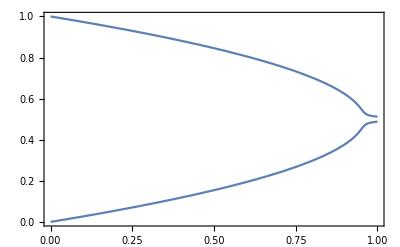

```mathematica
Plot[Chop[lista⟦All,1,2⟧/.{r-> 3.8283,yn1-> 0.01},10^-6],{xn1,0,1},Frame->True]
```

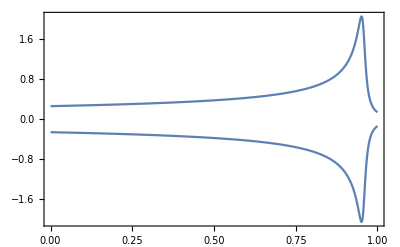

```mathematica
Plot[Chop[FullSimplify[D[lista⟦All,1,2⟧/.{ yn1-> 0.01,r-> 3.8283},xn1]/. xn1-> x],10^-3],{x,0,1},Frame->True]
```

```mathematica
Solve[yn1==im1,y]
```

{{y→-yn1/((-1+2 x) μ^3 (1-2 x μ+2 x^2 μ-2 x μ^2+2 x^2 μ^2+6 x^2 μ^3-12 x^3 μ^3+6 x^4 μ^3-4 x^3 μ^4+12 x^4 μ^4-12 x^5 μ^4+4 x^6 μ^4))}}

```mathematica
lista3=Solve[xn1==re1/. y->-yn1/((-1+2 x) μ^3 (1-2 x μ+2 x^2 μ-2 x μ^2+2 x^2 μ^2+6 x^2 μ^3-12 x^3 μ^3+6 x^4 μ^3-4 x^3 μ^4+12 x^4 μ^4-12 x^5 μ^4+4 x^6 μ^4)),x];
```

```mathematica
lista3⟦All,1,2⟧/. {μ-> 3.8283,xn1-> 0.51,yn1-> 0}
```

{0.499939,0.500061,0.491399,0.508601,0.329308,0.670692,0.329308,0.670692,0.227872,0.772128,0.154466,0.845534,0.154466,0.845534,0.0941256,0.905874,0.0421228,0.957877,0.0421228,0.957877,0.0114169,0.988583}

```mathematica
r1=x μ^3-x^2 μ^3+y^2 μ^3-x^2 μ^4+2 x^3 μ^4-x^4 μ^4+y^2 μ^4-6 x y^2 μ^4+6 x^2 y^2 μ^4-y^4 μ^4-x^2 μ^5+2 x^3 μ^5-x^4 μ^5+y^2 μ^5-6 x y^2 μ^5+6 x^2 y^2 μ^5-y^4 μ^5+2 x^3 μ^6-6 x^4 μ^6+6 x^5 μ^6-2 x^6 μ^6-6 x y^2 μ^6+36 x^2 y^2 μ^6-60 x^3 y^2 μ^6+30 x^4 y^2 μ^6-6 y^4 μ^6+30 x y^4 μ^6-30 x^2 y^4 μ^6+2 y^6 μ^6-x^4 μ^7+4 x^5 μ^7-6 x^6 μ^7+4 x^7 μ^7-x^8 μ^7+6 x^2 y^2 μ^7-40 x^3 y^2 μ^7+90 x^4 y^2 μ^7-84 x^5 y^2 μ^7+28 x^6 y^2 μ^7-y^4 μ^7+20 x y^4 μ^7-90 x^2 y^4 μ^7+140 x^3 y^4 μ^7-70 x^4 y^4 μ^7+6 y^6 μ^7-28 x y^6 μ^7+28 x^2 y^6 μ^7-y^8 μ^7/. {μ-> 3.8283,y-> 0}
```

0.+56.1071 x-1093.2 x^2+8370.2 x^3-31976.7 x^4+67094.1 x^5-78605.1 x^6+48206.1 x^7-12051.5 x^8

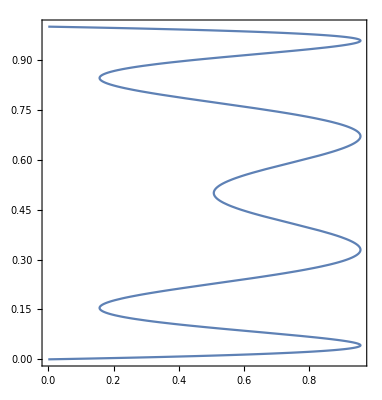

```mathematica
ParametricPlot[{r1,x},{x,0,1},Frame->True]
```

```mathematica
{a,b}/. {{a->1},{a-> 2}}
```

{{1,b},{2,b}}

```mathematica
map3=real/. y-> 0
ext=Solve[D[map3,x]==0,x]
ext/. μ-> 3.8283
d2 = D[map3,{x,2}]
```

x μ^3-x^2 μ^3-x^2 μ^4+2 x^3 μ^4-x^4 μ^4-x^2 μ^5+2 x^3 μ^5-x^4 μ^5+2 x^3 μ^6-6 x^4 μ^6+6 x^5 μ^6-2 x^6 μ^6-x^4 μ^7+4 x^5 μ^7-6 x^6 μ^7+4 x^7 μ^7-x^8 μ^7

{{x→1/2},{x→(μ-√(-2 μ+μ^2))/(2 μ)},{x→(μ+√(-2 μ+μ^2))/(2 μ)},{x→1/2 (1-√(1-2/μ-(2 √(-2 μ^3+μ^4))/μ^3))},{x→1/2 (1+√(1-2/μ-(2 √(-2 μ^3+μ^4))/μ^3))},{x→1/2 (1-√(1-2/μ+(2 √(-2 μ^3+μ^4))/μ^3))},{x→1/2 (1+√(1-2/μ+(2 √(-2 μ^3+μ^4))/μ^3))}}

{{x→1/2},{x→0.154466},{x→0.845534},{x→0.329308},{x→0.670692},{x→0.0421228},{x→0.957877}}

-2 μ^3-2 μ^4+12 x μ^4-12 x^2 μ^4-2 μ^5+12 x μ^5-12 x^2 μ^5+12 x μ^6-72 x^2 μ^6+120 x^3 μ^6-60 x^4 μ^6-12 x^2 μ^7+80 x^3 μ^7-180 x^4 μ^7+168 x^5 μ^7-56 x^6 μ^7

```mathematica
Table[{map3/.x->ext⟦j,1,2⟧,d2/. x-> ext⟦j,1,2⟧},{j,1,7}]/. μ-> 3.8283
```

{{0.507404,70.3137},{0.157276,187.548},{0.157276,187.548},{0.957075,-91.5356},{0.957075,-91.5356},{0.957075,-658.657},{0.957075,-658.657}}

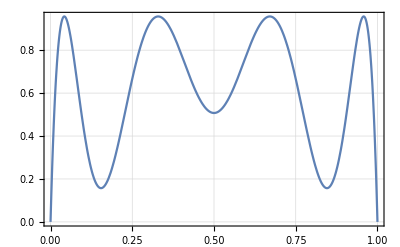

```mathematica
Plot[map3/.μ-> 3.8283,{x,0,1},GridLines->Automatic,Frame->True]
```

Se a derivada 2a é pequena (em módulo), então há mais pontos no eixo vertical do gráfico acima próximos ao mínimo, ou seja, uma faixa maior de pontos do Domínio é levada a uma pequena região na Imagem

```mathematica
{2/187.5481604163051,1/70.31370168640979,2/91.53558889912892+2/658.6570527658623}
```

{0.0106639,0.014222,0.0248859}

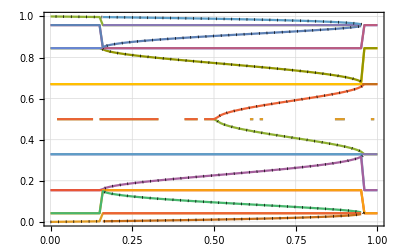

```mathematica
Show[ListPlot[Table[Table[{xn1,lista3⟦k,1,2⟧/. {μ-> 3.8283,yn1-> 0}},{xn1,0,1,0.01}],{k,1,22}],PlotRange->All,Frame->True,Joined->True,GridLines->Automatic],ParametricPlot[{map3/.μ-> 3.8283,x},{x,0,1},PlotStyle->{Black,Dotted,Thickness[0.005]}]]
```

```mathematica
Plot[lista3⟦All,1,2⟧/.{r-> 3.8283,yn1-> 0},{xn1,0,1},Frame->True]
```

$Aborted

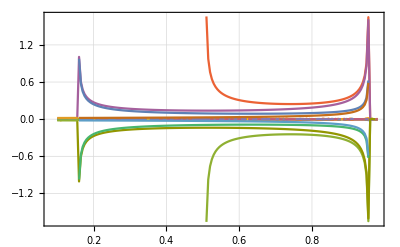

```mathematica
DPlot=ListPlot[Table[Table[{x,D[lista3⟦k,1,2⟧,xn1]/. {μ-> 3.8283,yn1-> 0,xn1-> x}},{x,0.1,0.98,0.005}],{k,1,22}],PlotRange->All,Frame->True,Joined->True,GridLines->Automatic]
```

```mathematica
Sum[Abs[D[lista3⟦s,1,2⟧,xn1]/. {μ-> 3.8283,yn1-> 0,xn1-> x}],{s,1,22}]/. x-> 0.76
```

1.12605

```mathematica
Table[{x,Sum[Abs[D[lista3⟦s,1,2⟧,xn1]/. {μ-> 3.8283,yn1-> 0,xn1-> x}],{s,1,22}]},{x,0,1,1/3}]
```

{{0,0.68646},{1/3,∞},{2/3,1.08466},{1,∞}}

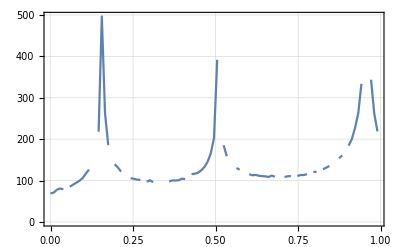

```mathematica
DSPlot=ListPlot[Table[{x,100Sum[Abs[D[lista3⟦s,1,2⟧,xn1]/. {μ-> 3.8283,yn1-> 0,xn1-> x}],{s,1,22}]},{x,0,1,1/103}],PlotRange->All,Frame->True,Joined->True,GridLines->Automatic]
```

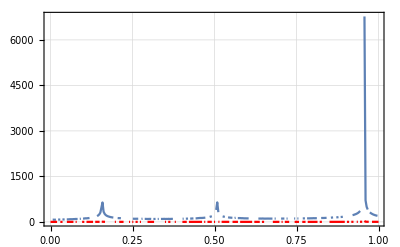

```mathematica
Show[DSPlot,ListPlot[Table[{x,Sum[Abs[D[lista3⟦s,1,2⟧,xn1]/. {μ-> 3.828,yn1-> 0,xn1-> x}],{s,1,22}]},{x,0,1,1/301}],PlotRange->All,Frame->True,Joined->True,GridLines->Automatic,PlotStyle->Red]]
```

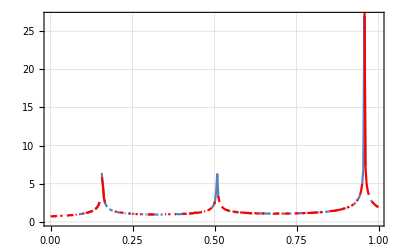
```mathematica
Show[-Graphics-,PlotRange-> {{0.92,0.98},{0,20}}]
```

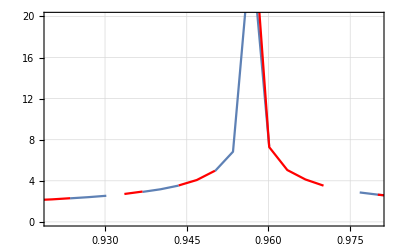

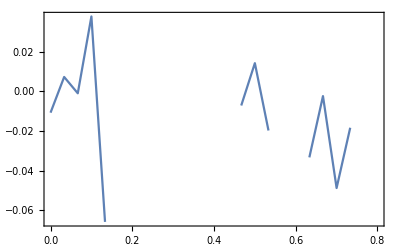

```mathematica
ListPlot[Table[{x,Sum[Abs[D[lista3⟦s,1,2⟧,xn1]/. {μ-> 3.8283,yn1-> 0,xn1-> x}],{s,1,22}]-Sum[Abs[D[lista3⟦s,1,2⟧,xn1]/. {μ-> 3.8282,yn1-> 0,xn1-> x}],{s,1,22}]},{x,0,1,1/30}],Frame->True,Joined->True]
```

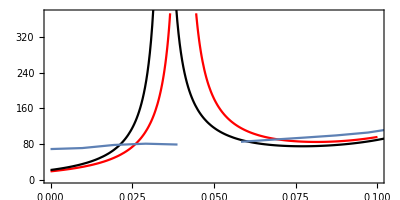

```mathematica
Show[Plot[{1000/Abs[D[real,x]]/. {x-> X,μ-> 3.8283,y-> 0.01}},{X,0,0.1},Frame->True,AspectRatio->1/2,PlotStyle->Red],
Plot[{1000/Abs[D[real,x]]/. {x-> X,μ-> 3.8283,y-> 0.02}},{X,0,1.1},Frame->True,AspectRatio->1/2,PlotStyle->Black],DSPlot]
```

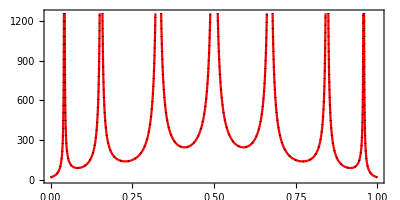

```mathematica
Show[Plot[{1000/Abs[D[real,x]]/. {x-> X,μ-> 3.8283,y-> 0}},{X,0,1},Frame->True,AspectRatio->1/2,PlotStyle->Red],
Plot[{1000/Abs[D[real,x]]/. {x-> X,μ-> 3.828,y-> 0}},{X,0,1},Frame->True,AspectRatio->1/2,PlotStyle->{Black,Dotted}]]
```

```mathematica
map3/. {x-> X,μ-> 3.8283}
```

56.1071 X-1093.2 X^2+8370.2 X^3-31976.7 X^4+67094.1 X^5-78605.1 X^6+48206.1 X^7-12051.5 X^8

```mathematica
Dmap3=D[real/.y-> 0,x];
Dim3=D[imag,y];
```

```mathematica
w1=Abs[1/Dmap3]/. {μ-> 3.8283}
w2=Abs[1/Dmap3]/. {μ-> 3.828}
```

1/Abs[56.1071-2186.4 x+25110.6 x^2-127907. x^3+335471. x^4-471631. x^5+337442. x^6-96412.1 x^7]

1/Abs[56.0939-2185.6 x+25099.4 x^2-127843. x^3+335294. x^4-471375. x^5+337257. x^6-96359.3 x^7]

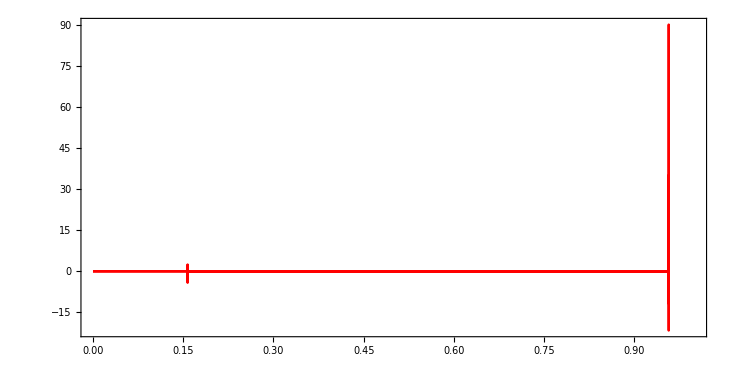

```mathematica
Show[ParametricPlot[{real/. {μ-> 3.8283,y-> 0},w1-w2},{x,0,1},Frame->True,AspectRatio->1/2,PlotStyle->Red],PlotRange-> {{0,1},Automatic}]
```

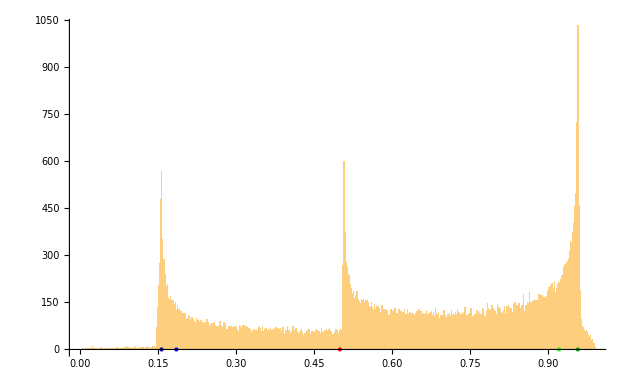
```mathematica
hist=-Graphics-;
```

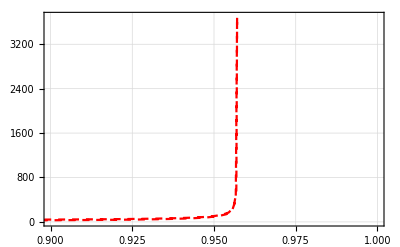

```mathematica
tail=ListPlot[Table[{real/. {μ-> 3.8283,y-> 0},300Abs[1/Dmap3]/. {μ-> 3.8283}},{x,0,0.1,0.001}],PlotStyle->{Red,Dashed},Joined->True,Frame->True,GridLines->Automatic,PlotRange->{{0.9,1},All}]
```

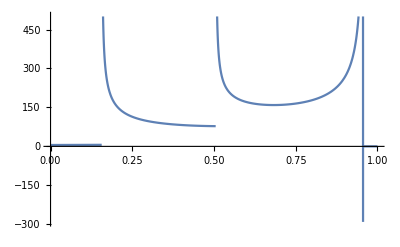

```mathematica
Plot[300pesototal[x],{x,0,1}]
```

```mathematica
Dmap3=D[real/.y-> 0.001,x];
Dim3=D[imag,y];
```

InterpolatingFunction::dmval: Input value {0.0000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

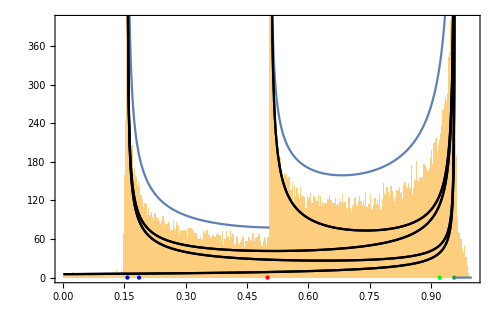

```mathematica
Show[hist,Plot[300pesototal[x],{x,0,1}],ParametricPlot[{real/. {μ-> 3.8283,y-> 0.001},300Abs[1/Dmap3]/. {μ-> 3.8283}},{x,0,1},MaxRecursion-> 10,AspectRatio->1/2,PlotStyle->Black,PlotRange->{0,10}],Frame->True,PlotRange-> {{0,1},{0,400}}]
```

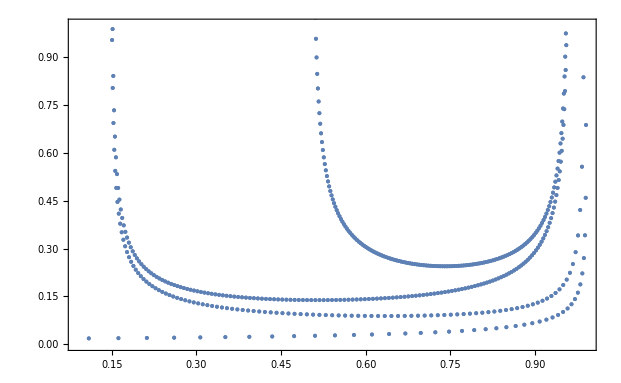

```mathematica
ListPlot[Table[{real/. {μ-> 3.8283,y-> 0.01},Abs[1/Dmap3]/. {μ-> 3.8283}},{x,0,1,0.001}],PlotRange->{All,{0,1}},Frame->True,Joined->False]
```

```mathematica
ListPlot3D[Table[{real/. {μ-> 3.8283,y-> 0.01},imag/. {μ-> 3.8283,y-> 0.01},Abs[1/Dmap3]/. {μ-> 3.8283}},{x,0,1,0.001}],PlotRange->{All,{-0.15,0.15},{0,0.5}}]
```

-Graphics3D-

```mathematica
d1=1/D[real/.y-> 0.02,x];
```

```mathematica
ListPlot3D[Table[{real/. {μ-> 3.8283,y-> 0.02},imag/. {μ-> 3.8283,y-> 0.02},Abs[d1]/. {μ-> 3.8283}},{x,0,1,0.001}],PlotRange->{All,{-0.15,0.15},{0,1}}]
```

-Graphics3D-

```mathematica
ListPlot3D[Table[{real/.μ-> 3.8283 ,imag/. {μ-> 3.8283},Abs[1/Dim3]/. {μ-> 3.8283}},{x,0,1,0.01},{y,-0.1,0.1,0.001}]]
```

-Graphics3D-

```mathematica
map3
```

x μ^3-x^2 μ^3-x^2 μ^4+2 x^3 μ^4-x^4 μ^4-x^2 μ^5+2 x^3 μ^5-x^4 μ^5+2 x^3 μ^6-6 x^4 μ^6+6 x^5 μ^6-2 x^6 μ^6-x^4 μ^7+4 x^5 μ^7-6 x^6 μ^7+4 x^7 μ^7-x^8 μ^7

```mathematica
ListPlot3D[Table[{real/. {μ-> 3.8283,y-> 0.01},imag/. {μ-> 3.8283,y-> 0.01},real/. {μ-> 3.8283,y-> 0.01}},{x,0,1,0.001}],PlotRange->{All,{-0.1,0.1},Automatic}]
```

-Graphics3D-

```mathematica
rea=real/. {μ-> 3.8283,y-> 0.01};
reb=real/. {μ-> 3.828,y-> 0.01};
dre=rea-reb;
ima=imag/. {μ-> 3.8283,y-> 0.01};
imb=imag/. {μ-> 3.828,y-> 0.01};
dim=ima-imb;
da=Abs[1/Dmap3]/. {μ-> 3.8283};
db=Abs[1/Dmap3]/. {μ-> 3.828};
dd = da - db;
```

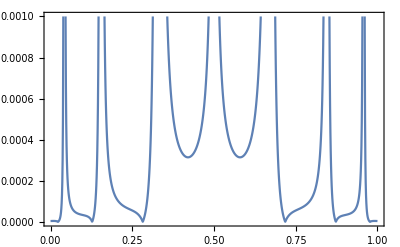

```mathematica
ListPlot[Table[{x, Abs[dd]},{x,0,1,0.001}],PlotRange->{0,10^-3},Frame->True,Joined->True]
```

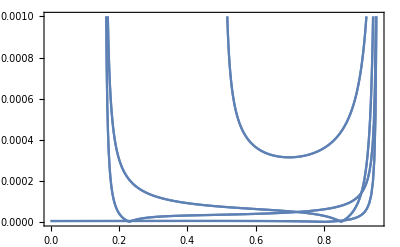

```mathematica
ListPlot[Table[{map3/. {μ-> 3.828}, Abs[dd]},{x,0,1,0.001}],PlotRange->{0,10^-3},Frame->True,Joined->True]
```

```mathematica
ListPlot3D[Table[{dre,dim,dd},{x,0,1,0.0001}],MeshFunctions->{#3&},PlotRange->{0,10}]
```

-Graphics3D-

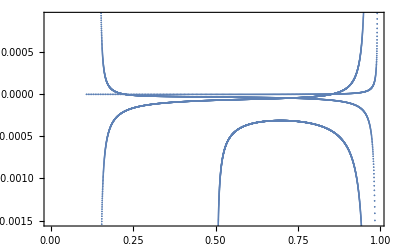

```mathematica
ListPlot[Table[{reb,dd},{x,0,1,0.0001}],Frame->True]
```

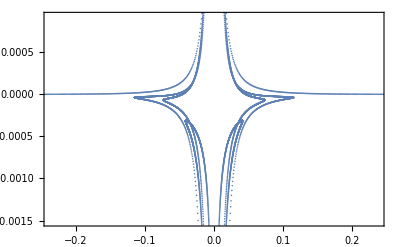

```mathematica
ListPlot[Table[{ima,dd},{x,0,1,0.0001}],Frame->True]
```

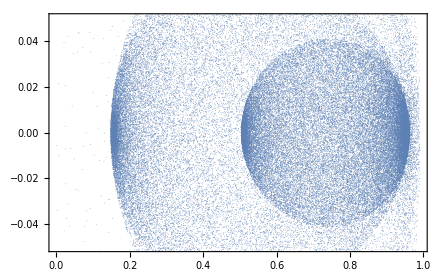

```mathematica
nuvem
```

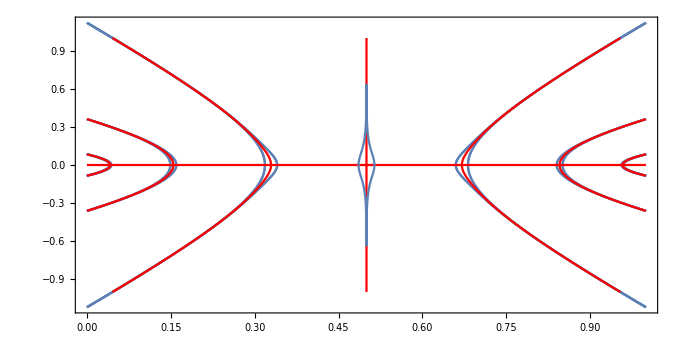

```mathematica
bands
```

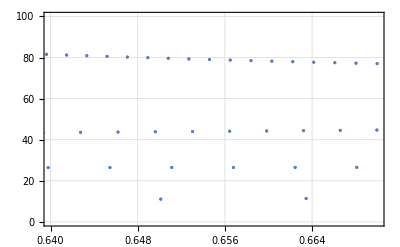

```mathematica
ListPlot[Table[{real/. {μ-> 3.8283,y-> 0},300Abs[1/Dmap3]/. {μ-> 3.8283}},{x,0,1,0.0005}],Frame->True,Joined->False,PlotRange->{{0.64,0.67},{0,100}},GridLines->Automatic]
```

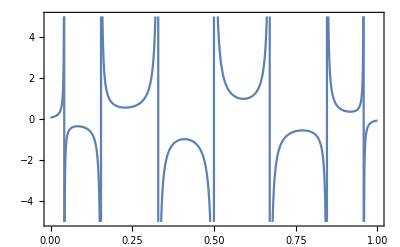

```mathematica
Plot[4/Dmap3/. μ-> 3.8283,{x,0,1},Frame->True]
```

```mathematica
peso[x_,μ_]=1/Dmap3/.x-> real/.y-> 0;
```

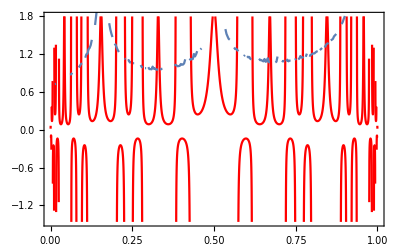

```mathematica
Show[Plot[peso[x,3.8283],{x,0,1},Frame->True,PlotStyle->Red],DSPlot]
```

```mathematica
peso[0.96,3.83]
```

0.831466

```mathematica
NIntegrate[√((peso[x,3.8283]x)^2),{x,0,1}]
```

0.341281

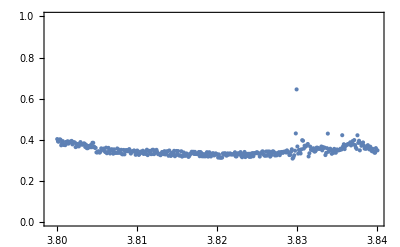

```mathematica
Block[{xi=0,xf=1},ListPlot[Table[{μ,1/(xf-xi)NIntegrate[√((peso[x,μ])^2)x,{x,xi,xf},PrecisionGoal->10]},{μ,3.8,3.84,0.0001}],Joined-> False,Frame->True,PlotRange->{0,1}]]
```

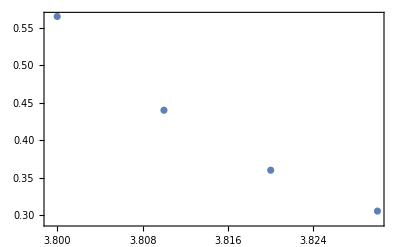

```mathematica
ListPlot[Table[{μ,√((peso[0.9,μ])^2)},{μ,3.8,3.835,0.01}],Joined-> False,Frame->True,PlotRange->All]
```

```mathematica
Table[{map3/.x->ext⟦j,1,2⟧,d2/. x-> ext⟦j,1,2⟧},{j,1,7}]/. μ-> 3.8283
```

{{0.507404,70.3137},{0.157276,187.548},{0.157276,187.548},{0.957075,-91.5356},{0.957075,-91.5356},{0.957075,-658.657},{0.957075,-658.657}}

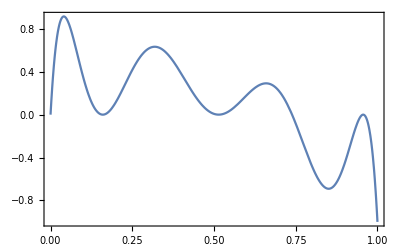

```mathematica
Plot[map3-x/. μ-> 3.8283,{x,0,1},Frame->True]
```

```mathematica
roots:=Solve[map3==x,x]/. μ-> 3.8283
```

```mathematica
Dmx=D[map3/. x-> y,y]/. y-> x
```

μ^3-2 x μ^3-2 x μ^4+6 x^2 μ^4-4 x^3 μ^4-2 x μ^5+6 x^2 μ^5-4 x^3 μ^5+6 x^2 μ^6-24 x^3 μ^6+30 x^4 μ^6-12 x^5 μ^6-4 x^3 μ^7+20 x^4 μ^7-36 x^5 μ^7+28 x^6 μ^7-8 x^7 μ^7

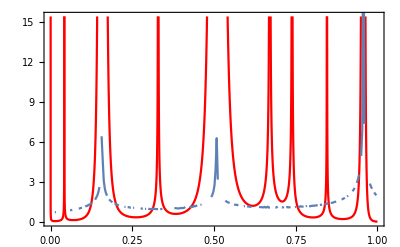

```mathematica
Show[Plot[Abs[1/(map3-x)1/Dmx]/.{ μ-> 3.8283},{x,0,1},Frame->True,PlotStyle->Red],DSPlot]
```

```mathematica
Abs[0.01/(map3-x)1/(D[map3/. x-> y,y]/. y-> x)]/.{ μ-> 3.8283,x-> 0.1}
```

0.0028219

```mathematica
D[map3/. x-> y,y]
```

μ^3-2 y μ^3-2 y μ^4+6 y^2 μ^4-4 y^3 μ^4-2 y μ^5+6 y^2 μ^5-4 y^3 μ^5+6 y^2 μ^6-24 y^3 μ^6+30 y^4 μ^6-12 y^5 μ^6-4 y^3 μ^7+20 y^4 μ^7-36 y^5 μ^7+28 y^6 μ^7-8 y^7 μ^7